# Изпит -2001261019

```mathematica
f[x_] := (√(x^3)-11Sin[x])/(1+(Cos[x])^2)-36
```

```mathematica
f[x]
```

-36+(√(x^3)-11 Sin[x])/(1+Cos[x]^2)

## 1. Да се намери общия брой на корените на уравнението.

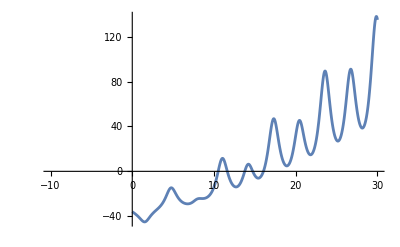

```mathematica
Plot[f[x],{x,-10,30}]
```

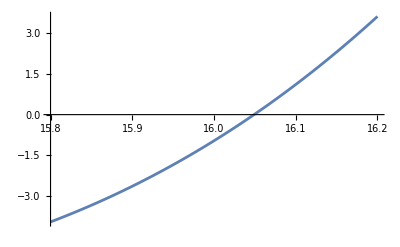

```mathematica
Plot[f[x],{x,15.8,16.2}]
```

## В) Да се направят 4 итерации по метода на разполовяването в инт [15.8;16.2]

```mathematica
f[x_] := (√(x^3)-11Sin[x])/(1+(Cos[x])^2)-36
```

```mathematica
a=15.8;b=16.2;
For[n=0,n<5,n++,
Print["n= ",n," a_n= ",a," b_n= ",b," m_n= ",m=(a+b)/2," f(m_n)= ",f[m]," ϵ_n= ",(b-a)/2];
If[f[m]>0,a=m,b=m]
]
```

n= 0 a_n= 15.8 b_n= 16.2 m_n= 16. f(m_n)= -0.964516 ϵ_n= 0.2

n= 1 a_n= 15.8 b_n= 16. m_n= 15.9 f(m_n)= -2.64225 ϵ_n= 0.1

n= 2 a_n= 15.8 b_n= 15.9 m_n= 15.85 f(m_n)= -3.34316 ϵ_n= 0.05

n= 3 a_n= 15.8 b_n= 15.85 m_n= 15.825 f(m_n)= -3.66085 ϵ_n= 0.025

n= 4 a_n= 15.8 b_n= 15.825 m_n= 15.8125 f(m_n)= -3.81171 ϵ_n= 0.0125

## Д) Оценка на грешката със зададена точност

```mathematica
f[x_] := (√(x^3)-11Sin[x])/(1+(Cos[x])^2)-36
```

```mathematica
Log2[(16.2-15.8)/0.0000001]-1
```

20.9316

## E) Условия за сходимост по метода на Нютон

### Проверка на първата производна

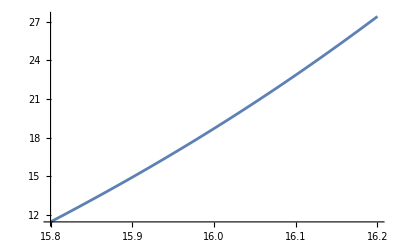

```mathematica
Plot[f'[x],{x,15.8,16.2}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [15.8; 16.2] са между 11 и 28. Следователно първата f’(x) > 0 в целия разглеждан интервал  [15.8; 16.2] .

### Проверка на втората производна

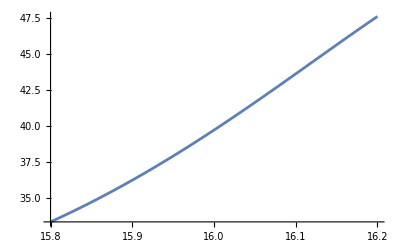

```mathematica
Plot[f''[x],{x,15.8,16.2}]
```

Извод: (2) Стойностите на първата производна в разглеждания интервал [15.8; 16.2] са между 33 и 48. Следователно втората f''(x) > 0 в целия разглеждан интервал [15.8; 16.2].

Извод: от (1) и (2) следва, че f'(x) и f''(x) са с постоянни знаци в разглеждания интервал [15.8; 16.2] => Методът на допирателните(Нютон) е сходящ.